```mathematica
dat=ReadList["global-data.dat"];
datSolitons=ReadList["solitons.txt"][[1]];
```

```mathematica
w=dat[[All,1]];
alpha=dat[[All,2]];
nr=dat[[All,3]];
Mint=-dat[[All,4]];
Jint=dat[[All,5]];
Q=dat[[All,6]];
MH =dat[[All,-9]];
JH =dat[[All,-8]];
Mass =dat[[All,-7]];
MInt=-dat[[All,-6]];
rh=dat[[All,-1]];
```

```mathematica
wSolitons = datSolitons[[All,1]];
MSolitons = datSolitons[[All,4]];
JSolitons = datSolitons[[All,5]];
```

```mathematica
len=Length[dat];
lenSolitons=Length[datSolitons];
solitonwM=ListPlot[Table[{wSolitons[[i]],MSolitons[[i]]},{i,1,lenSolitons}],PlotStyle->  Red];
```

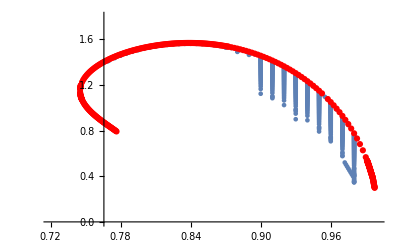

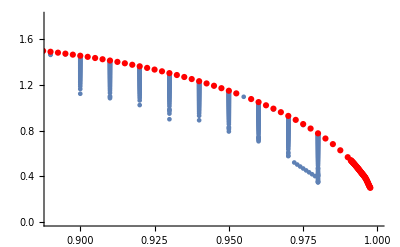

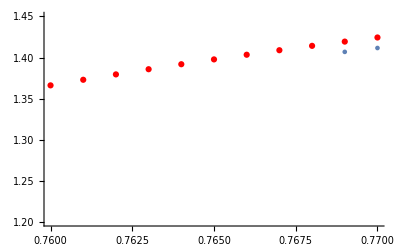

```mathematica
ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}]];
Show[%,solitonwM,PlotRange->{{0.72,1},{0,1.8}}]
ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}]];
Show[%,solitonwM,PlotRange->{{0.89,1},{0,1.8}}]
ListPlot[Table[{w[[i]],Mass[[i]]},{i,1,len}]];
Show[%,solitonwM,PlotRange->{{0.76,0.77},{1.2,1.45}}]
```

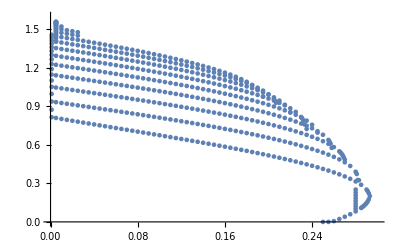

```mathematica
ListPlot[Table[{rh[[i]],Mint[[i]]},{i,1,len}],PlotRange->{{0.,0.3},{0.0,1.6}}]
```

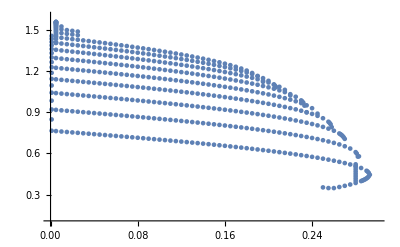

```mathematica
ListPlot[Table[{rh[[i]],Mass[[i]]},{i,1,len}],PlotRange->{{0.,0.3},{0.1,1.6}}]
```

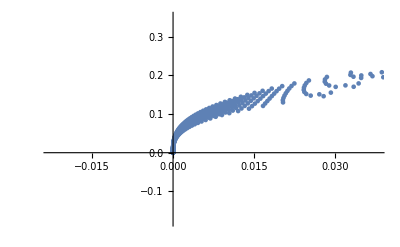

```mathematica
ListPlot[Table[{JH[[i]],MH[[i]]},{i,1,len}]]
```